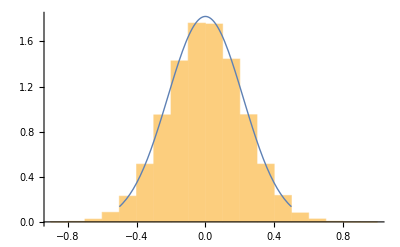

```mathematica
s=(3!)/n^3 J^2;
J=1;
n=5;
dist= 1/(√(2π s))ⅇ^(-x^2/(2s));
gauss=ProbabilityDistribution[dist,{x,-Infinity, Infinity}];
randomdata= RandomVariate[gauss,100000];
random := RandomVariate[gauss];
Show[Histogram[randomdata,20,"ProbabilityDensity"],Plot[PDF[gauss,x],{x,-0.5,0.5},PlotStyle->Thick]]
```

```mathematica
matJ = Normal@ SymmetrizedArray[_ :> random, {5,5,5,5},Antisymmetric[All]]//MatrixForm
```

((0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.11152 | 0.257323
0 | 0 | -0.11152 | 0 | 0.0152224
0 | 0 | -0.257323 | -0.0152224 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.11152 | -0.257323
0 | 0 | 0 | 0 | 0
0 | 0.11152 | 0 | 0 | -0.25288
0 | 0.257323 | 0 | 0.25288 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0.11152 | 0 | -0.0152224
0 | -0.11152 | 0 | 0 | 0.25288
0 | 0 | 0 | 0 | 0
0 | 0.0152224 | -0.25288 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0.257323 | 0.0152224 | 0
0 | -0.257323 | 0 | -0.25288 | 0
0 | -0.0152224 | 0.25288 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.11152 | -0.257323
0 | 0 | 0.11152 | 0 | -0.0152224
0 | 0 | 0.257323 | 0.0152224 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0.11152 | 0.257323
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-0.11152 | 0 | 0 | 0 | 0.22703
-0.257323 | 0 | 0 | -0.22703 | 0) | (0 | 0 | -0.11152 | 0 | 0.0152224
0 | 0 | 0 | 0 | 0
0.11152 | 0 | 0 | 0 | -0.22703
0 | 0 | 0 | 0 | 0
-0.0152224 | 0 | 0.22703 | 0 | 0) | (0 | 0 | -0.257323 | -0.0152224 | 0
0 | 0 | 0 | 0 | 0
0.257323 | 0 | 0 | 0.22703 | 0
0.0152224 | 0 | -0.22703 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.11152 | 0.257323
0 | 0 | 0 | 0 | 0
0 | -0.11152 | 0 | 0 | 0.25288
0 | -0.257323 | 0 | -0.25288 | 0) | (0 | 0 | 0 | -0.11152 | -0.257323
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0.11152 | 0 | 0 | 0 | -0.22703
0.257323 | 0 | 0 | 0.22703 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0.11152 | 0 | 0 | -0.25288
-0.11152 | 0 | 0 | 0 | 0.22703
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0.25288 | -0.22703 | 0 | 0 | 0) | (0 | 0.257323 | 0 | 0.25288 | 0
-0.257323 | 0 | 0 | -0.22703 | 0
0 | 0 | 0 | 0 | 0
-0.25288 | 0.22703 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | -0.11152 | 0 | 0.0152224
0 | 0.11152 | 0 | 0 | -0.25288
0 | 0 | 0 | 0 | 0
0 | -0.0152224 | 0.25288 | 0 | 0) | (0 | 0 | 0.11152 | 0 | -0.0152224
0 | 0 | 0 | 0 | 0
-0.11152 | 0 | 0 | 0 | 0.22703
0 | 0 | 0 | 0 | 0
0.0152224 | 0 | -0.22703 | 0 | 0) | (0 | -0.11152 | 0 | 0 | 0.25288
0.11152 | 0 | 0 | 0 | -0.22703
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
-0.25288 | 0.22703 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0.0152224 | -0.25288 | 0 | 0
-0.0152224 | 0 | 0.22703 | 0 | 0
0.25288 | -0.22703 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0
0 | 0 | -0.257323 | -0.0152224 | 0
0 | 0.257323 | 0 | 0.25288 | 0
0 | 0.0152224 | -0.25288 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0.257323 | 0.0152224 | 0
0 | 0 | 0 | 0 | 0
-0.257323 | 0 | 0 | -0.22703 | 0
-0.0152224 | 0 | 0.22703 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | -0.257323 | 0 | -0.25288 | 0
0.257323 | 0 | 0 | 0.22703 | 0
0 | 0 | 0 | 0 | 0
0.25288 | -0.22703 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | -0.0152224 | 0.25288 | 0 | 0
0.0152224 | 0 | -0.22703 | 0 | 0
-0.25288 | 0.22703 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0) | (0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0))

General::munfl: Exp[-833265.] is too small to represent as a normalized machine number; precision may be lost.